```mathematica
Needs["MaTeX`"]
SetDirectory[NotebookDirectory[]];
colors={ColorData["BlueGreenYellow"][0.1],ColorData["BlueGreenYellow"][0.4],ColorData["BlueGreenYellow"][0.8]};

SteadyState[R_]:=Module[{ps},
	ps = Table[(-1)^i Det[Drop[R,{2},{i}]],{i,Length@R}];
	ps /= Total[ps];
	ps
]

λcoeffs[R_,input_,e_] := Module[{pss,d,Rsp1,Rstall,pssstall,det,inv,c,λe0,λe1},
pss = SteadyState[R];
d = Length@R;
Rsp1 = R;(Rsp1[[input[[1]],#]]=1) &/@ Range[d];
det = Det[Rsp1];
inv = Inverse[Rsp1];
c = det-R[[input[[2]],input[[1]]]]det inv[[input[[1]],input[[2]]]]+R[[input[[1]],input[[2]]]]det inv[[input[[2]],input[[2]]]]//Expand//Chop;
λe1=1/c(-R[[e[[2]],e[[1]]]](-1)^(e[[1]]+input[[2]])Det[Drop[Rsp1,{input[[2]]},{e[[1]]}]]+R[[e[[1]],e[[2]]]](-1)^(e[[2]]+input[[2]])Det[Drop[Rsp1,{input[[2]]},{e[[2]]}]]);
Rstall = R-DiagonalMatrix[Diagonal[R]];Rstall[[input[[2]],input[[1]]]] = 0;Rstall[[input[[1]],input[[2]]]] = 0;
Rstall -= DiagonalMatrix[Total[Rstall]];
pssstall = SteadyState[Rstall];
λe0 = Rstall[[e[[2]],e[[1]]]]pssstall[[e[[1]]]]-Rstall[[e[[1]],e[[2]]]]pssstall[[e[[2]]]];
{λe0,λe1}
]
```

## Figure 1 - panels

```mathematica
Clear[r12,r21]
R={{0,r12,0,3.9,0,0},{r21,0,3.7,2.1,0,0},{0,4.2,0,2.7,0,3.1},{4.3,1.5,0.2,0,3.1,2.5},{0,0,0,0.4,0,4.5},{0,0,1.2,3.4,0.1,0}};
R-=DiagonalMatrix[Total[R]];
pss=SteadyState[R];
input={1,2};e={3,4};ep={6,5};
{λe0,λe1}=λcoeffs[R,input,e];
{λep0,λep1}=λcoeffs[R,input,ep];
ji=(R[[#2,#1]]pss[[#1]]-R[[#1,#2]]pss[[#2]]&@@@{input})[[1]];
je=(R[[#2,#1]]pss[[#1]]-R[[#1,#2]]pss[[#2]]&@@@{e})[[1]];
jep=(R[[#2,#1]]pss[[#1]]-R[[#1,#2]]pss[[#2]]&@@@{ep})[[1]];
jije=SortBy[Flatten[Table[{ji,je},{r12,0,3,.8},{r21,0,3,.8}],1],First];
jijep=SortBy[Flatten[Table[{ji,jep},{r12,0,3,.8},{r21,0,3,.8}],1],First];
```

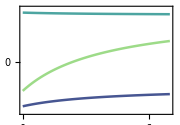

```mathematica
leg=Column[{
LineLegend[{colors[[1]]},{MaTeX["\\jmath_e",FontSize->14]}],
LineLegend[{colors[[2]]},{MaTeX["\\jmath_{e'}",FontSize->14]}]
},Spacings->-0.2];
plot1=Plot[Evaluate[{je,jep,ji}/.r12->1],{r21,0,7},PlotStyle->({#,Opacity[0.8],Thickness[0.01]}&/@colors[[;;3]]),
ImageSize->180,AspectRatio->.7,Axes->False,Frame->True,FrameStyle->Black,LabelStyle->{FontFamily->"Times"},FrameLabel->{{None,None},{MaTeX["r_{+i}",FontSize->16],None}},PlotRange->{{0,7},{-.35,.38}},Epilog->{Inset[MaTeX["\\jmath_{e'}",FontSize->16],Scaled[{.75,.85}]],Inset[MaTeX["\\jmath_{e}",FontSize->16],Scaled[{.75,.1}]],Inset[MaTeX["\\jmath_{i}",FontSize->14],Scaled[{.75,.56}]]},FrameTicks->{{Charting`ScaledTicks["Linear","Nice"][-.5,.5],Automatic},{Charting`ScaledTicks["Linear","Nice"][0,10],Automatic}}]
```

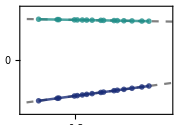

```mathematica
plot2=Show[Plot[λe0+λe1 x,{x,-5,5},PlotStyle->{Gray,Dashed}],
Plot[λep0+λep1 x,{x,-5,5},PlotStyle->{Gray,Dashed}],
ListPlot[{jije,jijep},Joined->True,PlotMarkers->{{Graphics[{colors[[1]],Disk[{0,0}]}],0.05},{Graphics[{colors[[2]],Disk[{0,0}]}],0.05}},PlotStyle->{{colors[[1]],Opacity[0.8],Thickness[0.01]},{colors[[2]],Opacity[0.8],Thickness[0.01]}}],
ImageSize->180,AspectRatio->.7,Axes->False,Frame->True,FrameStyle->Black,LabelStyle->{FontFamily->"Times"},FrameLabel->{{None,None},{MaTeX["\\jmath_i",FontSize->16],None}},PlotRange->{{-.45,.25},{-.45,.45}},Epilog->{Inset[MaTeX["\\jmath_{e'}",FontSize->16],Scaled[{.75,.73}]],Inset[MaTeX["\\jmath_{e}",FontSize->16],Scaled[{.75,.15}]]},FrameTicks->{{Charting`ScaledTicks["Linear","Nice"][-.5,1],Automatic},{Charting`ScaledTicks["Linear","Nice"][-1,.25],Automatic}}]
```

```mathematica
Export["jvsr.png",plot1,ImageResolution->600]
Export["jvsj.png",plot2,ImageResolution->600]
```

jvsr.png

jvsj.png

## Figure 2

OBS: This figure has a different style in the paper since it was generated using Python

```mathematica
susc[R_,pss_,Rstall_,pssstall_][input_,e_]:=Module[{res},
res=R[[e[[2]],e[[1]]]]pss[[e[[1]]]]-R[[e[[1]],e[[2]]]]pss[[e[[2]]]];
res-=Rstall[[e[[2]],e[[1]]]]pssstall[[e[[1]]]]-Rstall[[e[[1]],e[[2]]]]pssstall[[e[[2]]]];
res/=R[[input[[2]],input[[1]]]]pss[[input[[1]]]]-R[[input[[1]],input[[2]]]]pss[[input[[2]]]];
res
]
S=Import["sparse_matrix_bridge.mtx","MatrixMarket"];
Sbig=Import["sparse_matrix_big.mtx","MatrixMarket"];
```

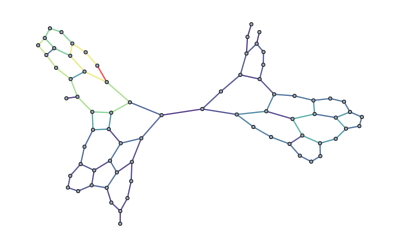

```mathematica
{NN,RR}=Dimensions[S];
kpv=Table[RandomReal[{.5,1}],{i,RR}];
kmv=Table[RandomReal[{.5,1}],{i,RR}];
V=Table[KroneckerDelta[S[[i,ρ]]-1] kmv[[ρ]]-KroneckerDelta[S[[i,ρ]]+1] kpv[[ρ]],{i,1,NN},{ρ,1,RR}];
input={42,45};
R =-S.Transpose[V];
pss=SteadyState[R];
Rstall=R;
Rstall[[input[[1]],input[[1]]]]+=Rstall[[input[[2]],input[[1]]]];
Rstall[[input[[2]],input[[2]]]]+=Rstall[[input[[1]],input[[2]]]];
Rstall[[input[[2]],input[[1]]]]=0;Rstall[[input[[1]],input[[2]]]]=0;
pssstall=SteadyState[Rstall];
Sundirected=MapIndexed[If[#1!=0,1,0]&,#,{2}]&@S;
el=EdgeList[IncidenceGraph[Sundirected]];
pos=Flatten[Position[el,input[[1]]<->input[[2]]]~Join~Position[el,input[[2]]<->input[[1]]]][[1]];
colorscheme=ColorData["BlueGreenYellow"][(ⅇ^(-6#)-1)/(ⅇ^-6-1)]&/@Table[Abs[susc[R,pss,Rstall,pssstall][input,e]],{e,el}];
colorscheme[[pos]]=Red;
estyle=MapIndexed[#1->{Thick,colorscheme[[First[#2]]]}&,el];
IncidenceGraph[Sundirected,EdgeStyle->estyle]
```

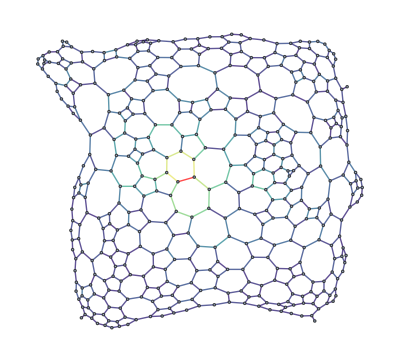

```mathematica
{NN,RR}=Dimensions[Sbig];
kpv=Table[RandomReal[{.5,1}],{i,RR}];
kmv=Table[RandomReal[{.5,1}],{i,RR}];
V=Table[KroneckerDelta[Sbig[[i,ρ]]-1] kmv[[ρ]]-KroneckerDelta[Sbig[[i,ρ]]+1] kpv[[ρ]],{i,1,NN},{ρ,1,RR}];
input={104,105};
R =-Sbig.Transpose[V];
pss=SteadyState[R];
Rstall=R;
Rstall[[input[[1]],input[[1]]]]+=Rstall[[input[[2]],input[[1]]]];
Rstall[[input[[2]],input[[2]]]]+=Rstall[[input[[1]],input[[2]]]];
Rstall[[input[[2]],input[[1]]]]=0;Rstall[[input[[1]],input[[2]]]]=0;
pssstall=SteadyState[Rstall];
Sundirected=MapIndexed[If[#1!=0,1,0]&,#,{2}]&@Sbig;
el=EdgeList[IncidenceGraph[Sundirected]];
pos=Flatten[Position[el,input[[1]]<->input[[2]]]~Join~Position[el,input[[2]]<->input[[1]]]][[1]];
colorscheme=ColorData["BlueGreenYellow"][(ⅇ^(-6#)-1)/(ⅇ^-6-1)]&/@Table[Abs[susc[R,pss,Rstall,pssstall][input,e]],{e,el}];
colorscheme[[pos]]=Red;
estyle=MapIndexed[#1->{Thick,colorscheme[[First[#2]]]}&,el];
IncidenceGraph[Sundirected,EdgeStyle->estyle]
```

## Appendix Figure: Myosin - V

```mathematica
Clear[P];
r21=10^5;r12=0.49;r32=4.6 10^3;r23=6.4 10^4;r43=3 10^3;r34=P 4.64;
r54=15.2;r45=3.35;r15=302.8;r51=0.62;r64=6.9 10^-2;r46=1.5 10^-2;r26=302.8;r62=1.27 10^-6 ;
R={{0,r12,0,0,r15,0},{r21,0,r23,0,0,r26},{0,r32,0,r34,0,0},{0,0,r43,0,r45,r46},{r51,0,0,r54,0,0},{0,r62,0,r64,0,0}};
R-=SetPrecision[DiagonalMatrix[Total[R]],50];
pss=SteadyState[R];
input={3,4};move={1,2};ATPmain={5,1};ATPfutile={6,2};
jPi=(R[[#2,#1]]pss[[#1]]-R[[#1,#2]]pss[[#2]]&@@@{input})[[1]];
jv=(R[[#2,#1]]pss[[#1]]-R[[#1,#2]]pss[[#2]]&@@@{move})[[1]];
jATP=Total[(R[[#2,#1]]pss[[#1]]-R[[#1,#2]]pss[[#2]]&@@@{ATPmain,ATPfutile})];
jATPfutile=Total[(R[[#2,#1]]pss[[#1]]-R[[#1,#2]]pss[[#2]]&@@@{ATPfutile})];
Λ0=λcoeffs[R,input,ATPmain][[1]]+λcoeffs[R,input,ATPfutile][[1]]-(λcoeffs[R,input,ATPmain][[2]]+λcoeffs[R,input,ATPfutile][[2]])/(λcoeffs[R,input,move][[2]])λcoeffs[R,input,move][[1]];
Λ1=(λcoeffs[R,input,ATPmain][[2]]+λcoeffs[R,input,ATPfutile][[2]])/(λcoeffs[R,input,move][[2]]);
tab=Table[{jv,jATP},{P,0,10^2,10}];
{Λ0,Λ1}
```

{8.36448×10^-11,1.00459}

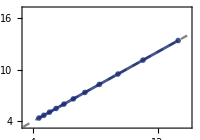

```mathematica
plotmyosin=Show[Plot[Λ0+Λ1 x,{x,0,15},PlotStyle->{Gray,Dashed}],ListPlot[tab,Joined->True,PlotMarkers->{{Graphics[{colors[[1]],Disk[{0,0}]}],0.05}},PlotStyle->{{colors[[1]],Opacity[0.8],Thickness[0.01]}}],PlotRange->{{3.5,14},{3.5,17}},ImageSize->200,AspectRatio->.7,Axes->False,Frame->True,FrameStyle->Black,LabelStyle->{FontFamily->"Times"},FrameLabel->{{MaTeX["\\mathcal{J}_\\text{ATP}",FontSize->12],None},{MaTeX["\\jmath_m",FontSize->12],None}},FrameTicks->{{Charting`ScaledTicks["Linear","Nice"][4,18],Automatic},{Charting`ScaledTicks["Linear","Nice"][4,17],Automatic}}]
```

```mathematica
Export["myosin_currents.png",plotmyosin,ImageResolution->600]
```

myosin_currents.png

## SM’s Figure 1

```mathematica
Clear[r21,r12]
R=({{0, r12, 0, 2, 0, 0}, {r21, 0, 10, 5, 0, 0}, {0, 5, 0, 3, 0, 1}, {3, 2, 2, 7, 2, 2}, {0, 3, 0, 3, 0, 1}, {0, 0, 1, 5, 3, 0}});
R-=DiagonalMatrix[Total[R]];pss=SteadyState[R];
input={1,2};e={6,5};
r12i=3;r21i=2;Ri=R/.{r12->r12i,r21->r21i};
pssi=pss/.{r12->r12i,r21->r21i};
jii=r21i pssi[[1]]-r12i pssi[[2]];
jei=R[[e[[2]],e[[1]]]] pssi[[e[[1]]]]-R[[e[[1]],e[[2]]]]pssi[[e[[2]]]];
{λe0,λe1}=λcoeffs[R,input,e];
tvec={0,.1,.2,.3,.5,100};tveclabel=(ToString[#]&/@tvec[[;;-2]])~Join~{"∞"};
repmax=100;
r12vec=Table[RandomReal[{0,5}],{rep,repmax}];r21vec=Table[RandomReal[{0,5}],{rep,repmax}];
vecs={};Do[
vec={};Do[
r12f=r12vec[[rep]];r21f=r21vec[[rep]];
Rf=R/.{r12->r12f,r21->r21f};
jif=r21f (MatrixExp[t Rf].pssi)[[1]]-r12f (MatrixExp[t Rf].pssi)[[2]];
jef=R[[e[[2]],e[[1]]]] (MatrixExp[t Rf].pssi)[[e[[1]]]]-R[[e[[1]],e[[2]]]](MatrixExp[t Rf].pssi)[[e[[2]]]];
AppendTo[vec,{jif,jef}//Chop];
,{rep,repmax}];
AppendTo[vecs,vec];
,{t,tvec}]
(*Laplace*)
svec={};Do[
r12f=r12vec[[rep]];r21f=r21vec[[rep]];
Rf=R/.{r12->r12f,r21->r21f};
LaplaceProp=-Inverse[Rf-s IdentityMatrix[Length@Rf]];
jifs=r21f (LaplaceProp.pssi)[[1]]-r12f (LaplaceProp.pssi)[[2]];
jefs=R[[e[[2]],e[[1]]]] (LaplaceProp.pssi)[[e[[1]]]]-R[[e[[1]],e[[2]]]](LaplaceProp.pssi)[[e[[2]]]];
AppendTo[svec,{jifs,jefs}]
,{rep,repmax}];
svals=Range[0.1,1,.1];
svecs=(svec/.s->#)&/@svals;
```

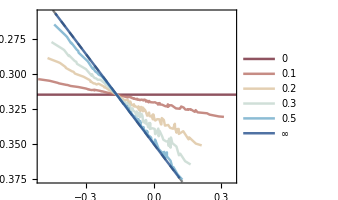
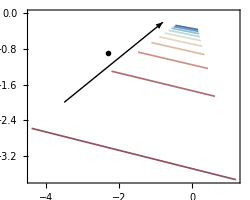

```mathematica
leg=LineLegend[(Directive[#,Thickness[0.005],Opacity[.8]]&/@Table[ColorData["RedBlueTones",i/(1(Length[vecs]-1))],{i,0,Length[vecs]-1}]),tveclabel,Spacings->.5,LabelStyle->{FontFamily->"Times New Roman"},LegendLayout->{"Column",2}];
p1hold=ListLinePlot[SortBy[#,First]&/@vecs,PlotRange->{{-.5,.35},All},PlotStyle->(Directive[#,Thickness[0.007],Opacity[.8]]&/@Table[ColorData["RedBlueTones",i/(1(Length[vecs]-1))],{i,0,Length[vecs]-1}]),Frame->True,FrameStyle->Black,(*PlotLegends->Placed[tveclabel,Scaled[{.87,.63}]],*)AspectRatio->.8,ImageSize->250,Axes->False,FrameLabel->{MaTeX["\\jmath_1(t)",FontSize->14],MaTeX["\\jmath_e(t)",FontSize->14]},LabelStyle->{FontFamily->"Times New Roman"},GridLines->{{jii},{jei}},Epilog->Inset[leg,Scaled[{.7,.8}]]];
p1=Show[Plot[λe0+λe1 x,{x,-1,1},PlotStyle->{Gray,Dashed}],p1hold,Options[p1hold]];
p2=ListLinePlot[SortBy[#,First]&/@svecs,PlotStyle->(Directive[#,Thickness[0.005],Opacity[.8]]&/@Table[ColorData["RedBlueTones",i/(1(Length[svals]-1))],{i,0,Length[svals]-1}]),Frame->True,FrameStyle->Black(*,PlotLegends->Placed[ToString[#]&/@svals,Scaled[{.87,.63}]]*),Axes->False,Epilog->{AbsoluteThickness[1],Arrowheads[.04],Arrow[{{-3.5,-2},{-.8,-.2}}],Text[MaTeX["\\varsigma",FontSize->14],{-2.3,-.9}]},AspectRatio->.8,ImageSize->250,FrameLabel->{MaTeX["\\hat{\\jmath}_1(\\varsigma)",FontSize->14],MaTeX["\\hat{\\jmath}_e(\\varsigma)",FontSize->14]},LabelStyle->{FontFamily->"Times New Roman"},PlotRange->All];
Row[{p1,p2}]
```

```mathematica
Export["transient.png",p1,ImageResolution->500]
Export["laplace.png",p2,ImageResolution->500]
```

transient.png

laplace.png